## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p380";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## longest times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
saveFolderLT="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p380/";
```

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.016 ,0.01, 0.008 ,0.0063 ,0.005 ,0.00385, 0.0031 ,0.0028, 0.0025 ,0.0022 ,0.002 ,0.0018};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000,0.00180000}

```mathematica
wtlist={0.,50000.,60000.,70000.,80000.,90000.,100000.};
```

```mathematica
wtliststring=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlist
```

{0.00,50000.00,60000.00,70000.00,80000.00,90000.00,100000.00}

```mathematica
wtlistLongest={10000.,10000.,10000.,10000.,10000.,10000.,10000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.};
```

```mathematica
wtlistLongestString=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlistLongest
```

{10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00}

```mathematica
{"0.00","50000.00","60000.00","70000.00","80000.00","90000.00","100000.00}
```

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolderLT,"SISFCRSISF_N4096_p3.8000_T",Tstring[[16]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,7}],{idx,0,2}];
```

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolderLT,"overlapCRoverlap_N4096_p3.8000_T",Tstring[[15]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,7}],{idx,0,2}];
```

```mathematica
SISFLT[[1,1,1]]
```

1.

```mathematica
timeLongest=Table[testdata=Import[StringJoin[saveFolderLT,"glassyDynamics_N4096_p3.8000_T",Tstring[[16]],"_waitingTime",wtliststring[[wt]],"_idx1.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,7}];
```

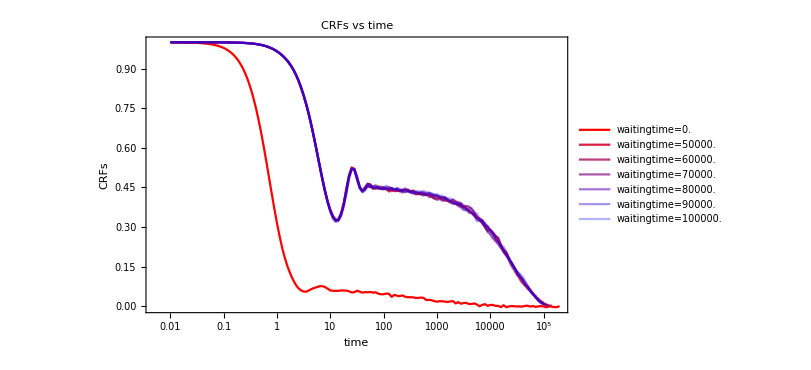

```mathematica
CRFswaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[SISF[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]}],{wt,7}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,7}]]
```

```mathematica
Normal[overlap[[1,7,1]]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999756,0.996338,0.991455,0.986328,0.971436,0.958496,0.94165,0.925537,0.901611,0.887695,0.885986,0.884766,0.883301,0.891357,0.893066,0.88208,0.868652,0.843994,0.835693,0.835449,0.820313,0.825195,0.811768,0.801025,0.79541,0.782959,0.773682,0.755371,0.73999,0.729736,0.696777,0.707031,0.717529,0.744385,0.733643,0.741699,0.764404,0.753662,0.731934,0.7229,0.722656,0.720215,0.715332,0.709717,0.675537,0.697998,0.751709,0.708008,0.622559,0.654053,0.634277,0.5896,0.615479,0.567383,0.594727,0.578613,0.551758,0.57959,0.558594,0.537354,0.44165,0.522461,0.506348,0.507324,0.461182,0.461426,0.428467,0.368408,0.26709,0.257813,0.250977,0.276123,0.219727,0.194092,0.191895,0.196777,0.147461,0.111572,0.088623,0.064209,0.0617676,0.0495605,0.0456543,0.0461426,0.043457,0.0412598,0.0373535,0.0322266}

```mathematica
Export["/home/chengling/Research/updates/02012024/CRFswaitTimeLT.jpeg",CRFswaitTimeLT,ImageResolution->600];
```

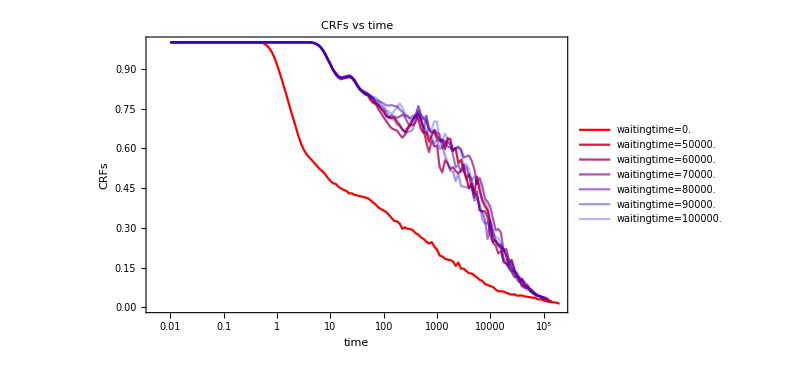

```mathematica
CRoverlapwaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[overlap[[idx,wt,1,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]}],{wt,7}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,7}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolderLT,"overlapCRoverlap_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
Normal[overlap[[1,1,1]]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999023,0.996826,0.989746,0.974121,0.959961,0.929443,0.893066,0.844727,0.800049,0.752686,0.704346,0.654053,0.602295,0.560303,0.519531,0.47583,0.443115,0.418457,0.38623,0.351563,0.315674,0.284424,0.260254,0.229248,0.211426,0.191406,0.172363,0.144531,0.123779,0.112793,0.095459,0.0808105,0.0744629,0.057373,0.057373,0.0495605,0.0383301,0.0334473,0.0297852,0.0263672,0.0234375,0.0178223,0.0214844,0.0202637,0.0161133,0.0161133,0.0109863,0.0107422,0.0090332,0.00830078,0.0090332,0.00732422,0.00610352,0.00341797,0.00415039,0.00195313,0.00366211,0.00268555,0.00244141,0.00146484,0.000976563,0.0012207,0.00219727,0.0012207,0.000488281,0.000488281}

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolderLT,"SISFCRSISF_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
CRoverlapMean=Table[Table[Mean[Table[overlap[[T,i,2,rec]],{i,3}]],{rec,Length[overlap[[T,1,1]]]}],{T,Length[Tlist]}];
overlapMean=Table[Table[Mean[Table[overlap[[T,i,1,rec]],{i,3}]],{rec,Length[overlap[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
CRSISFMean=Table[Table[Mean[Table[SISF[[T,i,2,rec]],{i,3}]],{rec,Length[SISF[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
SISFMean=Table[Table[Mean[Table[SISF[[T,i,1,rec]],{i,3}]],{rec,Length[SISF[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
testdata=Import[StringJoin[saveFolderLT,"glassyDynamics_N4096_p3.8000_T",Tstring[[16]],"_waitingTime",wtlistLongestString[[16]],"_idx1.nc"],"Data"];time=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

```mathematica
overlapMean[[1]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999837,0.999023,0.996501,0.990153,0.977458,0.959473,0.93042,0.895833,0.849935,0.802897,0.758219,0.706787,0.657633,0.607096,0.560872,0.516357,0.47583,0.441325,0.411865,0.380534,0.350993,0.317708,0.28597,0.256104,0.226888,0.20516,0.181071,0.161051,0.143311,0.12557,0.110677,0.0948079,0.0863444,0.0724284,0.0664876,0.0588379,0.0515951,0.0432129,0.0367025,0.0308431,0.0303548,0.0264486,0.0206706,0.0209147,0.019043,0.0152181,0.0142415,0.0117188,0.010498,0.00952148,0.00756836,0.00724284,0.00651042,0.00553385,0.00455729,0.00382487,0.00358073,0.00366211,0.00309245,0.00333659,0.0016276,0.00170898,0.00260417,0.0016276,0.00170898,0.000895182,0.000651042}

```mathematica
Log10[timeLongest[[52]]]
```

1.80003

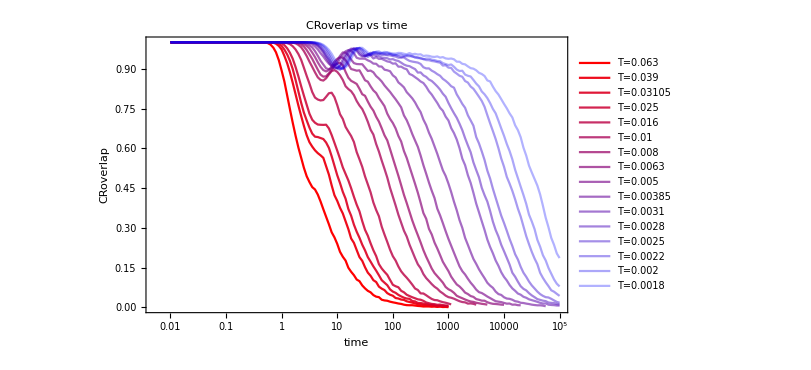

```mathematica
CRoverlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[TlistLongest]}],PlotLegends->Table["T="<>ToString[TlistLongest[[T]]],{T,Length[TlistLongest]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True]
```

```mathematica
fitCROverlapStartPos={46,47,49,50,54,58,60,62,64,67,69,75,75,75,75,75}
```

{46,47,49,50,54,58,60,62,64,67,69,75,75,75,75,75}

```mathematica
fitsCROverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRoverlapMean[[T,rec]]]},{rec,fitOverlapStartPos[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCROverlap
```

{FittedModel[0.989954 ⅇ^(-0.405764 t^0.540588)],FittedModel[0.989987 ⅇ^(-0.219979 t^0.610297)],FittedModel[0.989991 ⅇ^(-0.166806 t^0.629919)],FittedModel[0.989993 ⅇ^(-0.120782 t^0.655342)],FittedModel[0.989996 ⅇ^(-0.0620973 t^0.697532)],FittedModel[0.989998 ⅇ^(-0.0254952 t^0.752693)],FittedModel[0.989998 ⅇ^(-0.0178276 t^0.751013)],FittedModel[0.989998 ⅇ^(-0.0116682 t^0.749091)],FittedModel[0.989999 ⅇ^(-0.00699925 t^0.75636)],FittedModel[0.989998 ⅇ^(-0.00399848 t^0.7572)],FittedModel[0.981051 ⅇ^(-0.00147709 t^0.792904)],FittedModel[0.989982 ⅇ^(-0.00132008 t^0.765856)],FittedModel[0.989848 ⅇ^(-0.000697377 t^0.798052)],FittedModel[0.976271 ⅇ^(-0.000211347 t^0.857844)],FittedModel[0.9672 ⅇ^(-0.00014312 t^0.861099)],FittedModel[0.964888 ⅇ^(-0.0000634493 t^0.887014)]}

```mathematica
tauCROverlapfits=Table[fitsCROverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{5.30434,11.9547,17.1689,25.1649,53.7381,130.954,213.173,380.59,706.486,1469.16,3714.56,5750.6,9021.89,19230.9,29134.5,53982.2}

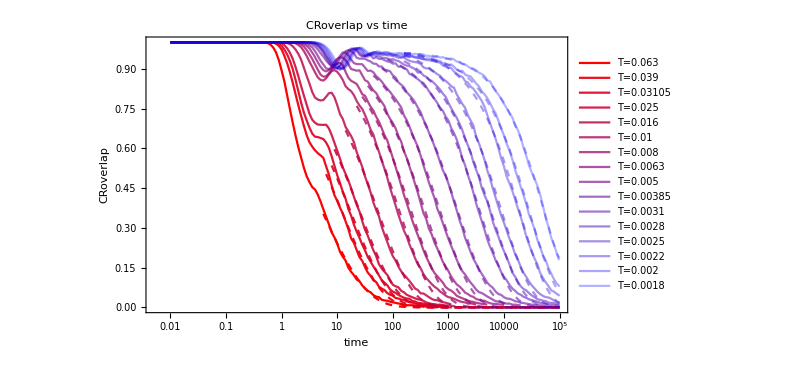

```mathematica
Show[CRoverlapPlot,Table[LogLinearPlot[fitsCROverlap[[T]][x],{x,time[[fitCROverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

### overlap

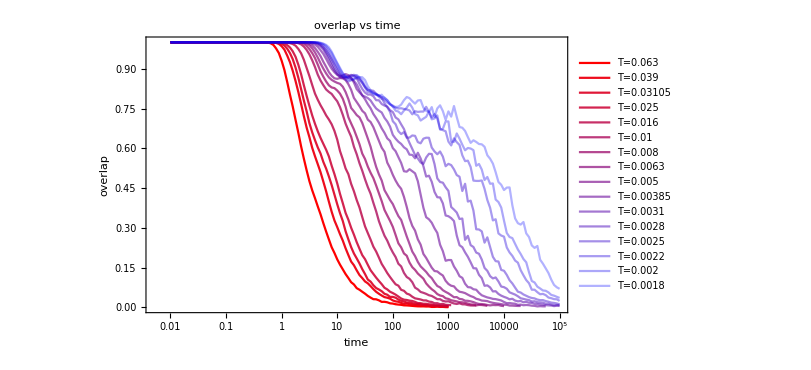

```mathematica
overlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[TlistLongest]}],PlotLegends->Table["T="<>ToString[TlistLongest[[T]]],{T,Length[TlistLongest]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True]
```

```mathematica
fitOverlapStartPos={46,47,49,50,54,58,60,62,64,67,69,75,75,75,75,75}
```

{46,47,49,50,54,58,60,62,64,67,69,75,75,75,75,75}

```mathematica
fitsOverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[overlapMean[[T,rec]]]},{rec,fitOverlapStartPos[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.9>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsOverlap
```

{FittedModel[0.899949 ⅇ^(-0.416692 t^0.570721)],FittedModel[0.899984 ⅇ^(-0.257924 t^0.620357)],FittedModel[0.899988 ⅇ^(-0.18419 t^0.675023)],FittedModel[0.899991 ⅇ^(-0.158969 t^0.656324)],FittedModel[0.899992 ⅇ^(-0.0998525 t^0.67266)],FittedModel[0.899995 ⅇ^(-0.0642449 t^0.668794)],FittedModel[0.899995 ⅇ^(-0.0638978 t^0.608194)],FittedModel[0.899996 ⅇ^(-0.0488928 t^0.612934)],FittedModel[0.899998 ⅇ^(-0.0287827 t^0.652699)],FittedModel[0.899993 ⅇ^(-0.0263337 t^0.587713)],FittedModel[0.835829 ⅇ^(-0.0154975 t^0.586561)],FittedModel[0.860669 ⅇ^(-0.01795 t^0.537109)],FittedModel[0.733526 ⅇ^(-0.00228932 t^0.718824)],FittedModel[0.830126 ⅇ^(-0.00269093 t^0.656634)],FittedModel[0.784529 ⅇ^(-0.00107861 t^0.721048)],FittedModel[0.822266 ⅇ^(-0.00157456 t^0.642418)]}

```mathematica
tauOverlapfits=Table[fitsOverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{4.63605,8.88505,12.259,16.4782,30.7319,60.6114,92.052,137.561,229.49,486.987,1217.13,1780.79,4710.57,8204.43,13032.7,23065.1}

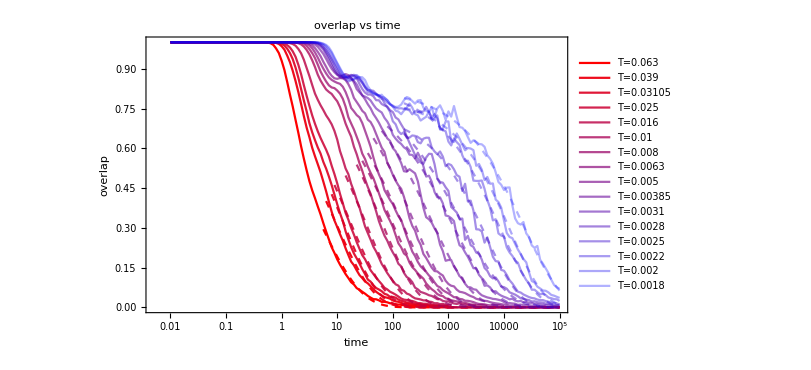

```mathematica
Show[overlapPlot,Table[LogLinearPlot[fitsOverlap[[T]][x],{x,time[[fitOverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlap.jpeg",Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

#### CRSISF

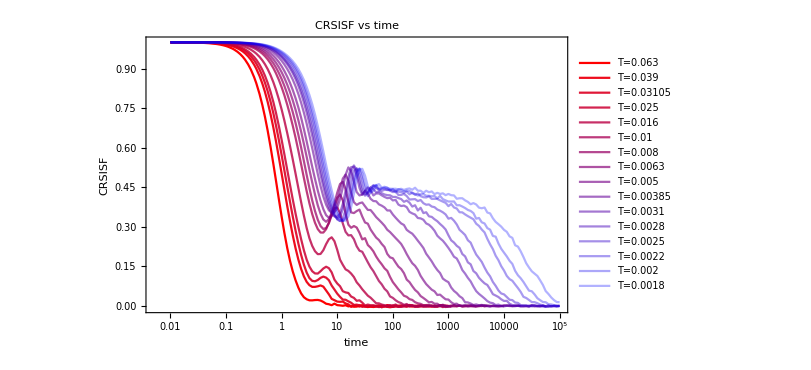

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFMean[[T,rec]]},{rec,Length[CRSISFMean[[T]]]}],{T,Length[TlistLongest]}],PlotLegends->Table["T="<>ToString[TlistLongest[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

```mathematica
fitCRSISFStartNum={5.223562384371017,5.9897781249014574,7.27896687589429,8.18350888496611,13.306468818755748,20.44545362547953,26.848904506044427,34.59556960139557,43.716132675532066,60.85859262176283,78.39053286118767,88.0976485665916,99.02222096719747,99.03378947388394,99.04535933208875,99.04535933208875};
```

```mathematica
fitCRSISFStartPos=Table[Position[time,_?(#>fitCRSISFStartNum[[i]]&)][[1,1]],{i,16}]
```

{46,47,49,50,54,58,60,62,64,67,69,70,71,71,71,71}

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRSISFMean[[T,rec]]]},{rec,fitCRSISFStartPos[[T]],Length[CRSISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.5>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCRSISF
```

{FittedModel[0.340381 ⅇ^(-1.00001 t^0.677533)],FittedModel[0.496301 ⅇ^(-0.456676 t^0.855332)],FittedModel[0.498335 ⅇ^(-0.294188 t^0.898438)],FittedModel[0.32385 ⅇ^(-0.173576 t^0.884069)],FittedModel[0.406731 ⅇ^(-0.0929931 t^0.899763)],FittedModel[0.464852 ⅇ^(-0.0420802 t^0.899866)],FittedModel[0.423376 ⅇ^(-0.0238347 t^0.899671)],FittedModel[0.446069 ⅇ^(-0.0208647 t^0.822498)],FittedModel[0.466417 ⅇ^(-0.0146888 t^0.787069)],FittedModel[0.453613 ⅇ^(-0.00644902 t^0.808849)],FittedModel[0.433253 ⅇ^(-0.00154885 t^0.884168)],FittedModel[0.449899 ⅇ^(-0.00207043 t^0.797151)],FittedModel[0.444015 ⅇ^(-0.000571504 t^0.899985)],FittedModel[0.444999 ⅇ^(-0.000278927 t^0.899993)],FittedModel[0.441695 ⅇ^(-0.000191544 t^0.89997)],FittedModel[0.445772 ⅇ^(-0.000115049 t^0.892181)]}

```mathematica
tauCRSISFfits=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[TlistLongest]}]
```

{0.999983,2.50014,3.9034,7.24834,14.011,33.8089,63.6444,110.477,213.261,510.714,1507.02,2327.63,4012.09,8901.97,13519.1,26010.6}

```mathematica
Length[TlistLongest]
```

5

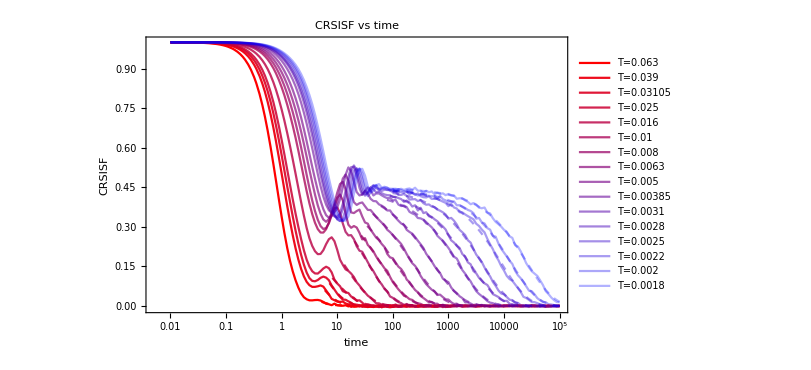

```mathematica
Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,fitCRSISFStartNum[[T]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRSISF_p380.jpeg",Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

#### SISF

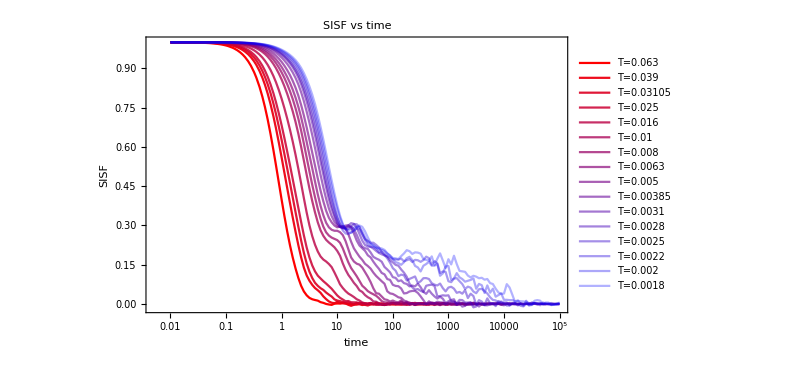

```mathematica
SISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],SISFMean[[T,rec]]},{rec,Length[SISFMean[[T]]]}],{T,Length[TlistLongest]}],PlotLegends->Table["T="<>ToString[TlistLongest[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```

```mathematica
fitSISFStartPos={46,47,49,50,54,58,60,62,64,69,69,75,75,75,75,75}
```

{46,47,49,50,54,58,60,62,64,69,69,75,75,75,75,75}

```mathematica
fitsSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISFMean[[T,rec]]]},{rec,fitSISFStartPos[[T]],Length[SISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.5>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsSISF
```

{FittedModel[0.389695 ⅇ^(-1.21686 t^0.84734)],FittedModel[0.471656 ⅇ^(-0.667003 t^0.87804)],FittedModel[0.475772 ⅇ^(-0.590409 t^0.769207)],FittedModel[0.492489 ⅇ^(-0.36901 t^0.862963)],FittedModel[0.401057 ⅇ^(-0.192664 t^0.896631)],FittedModel[0.496577 ⅇ^(-0.122052 t^0.897377)],FittedModel[0.294387 ⅇ^(-0.0722042 t^0.894352)],FittedModel[0.499604 ⅇ^(-0.06711 t^0.899403)],FittedModel[0.363914 ⅇ^(-0.0360303 t^0.898127)],FittedModel[0.192066 ⅇ^(-0.0290289 t^0.742003)],FittedModel[0.191781 ⅇ^(-0.0249584 t^0.680195)],FittedModel[0.146665 ⅇ^(-0.00995751 t^0.755348)],FittedModel[0.115751 ⅇ^(-0.00128434 t^0.899582)],FittedModel[0.210123 ⅇ^(-0.00352549 t^0.746696)],FittedModel[0.183986 ⅇ^(-0.00355128 t^0.688254)],FittedModel[0.219591 ⅇ^(-0.00369183 t^0.656228)]}

```mathematica
tauSISFfits=Table[fitsSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.793236,1.58599,1.98386,3.1748,6.27555,10.4212,18.8918,20.1574,40.4621,117.936,227.173,446.924,1637.08,1926.85,3623.88,5095.46}

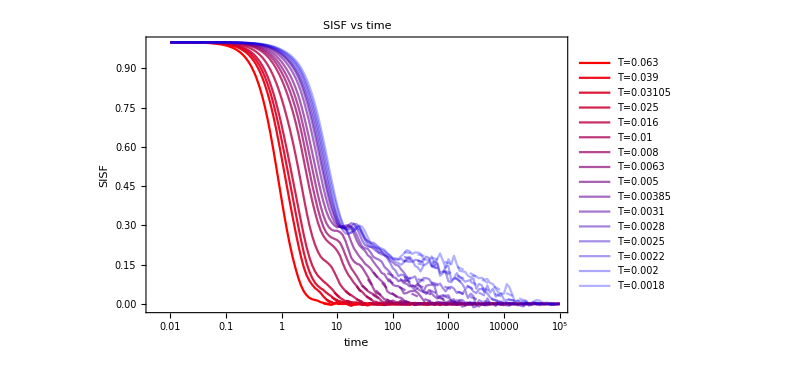

```mathematica
Show[SISFPlot,Table[LogLinearPlot[fitsSISF[[T]][x],{x,time[[fitSISFStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

#### Tau Alphas

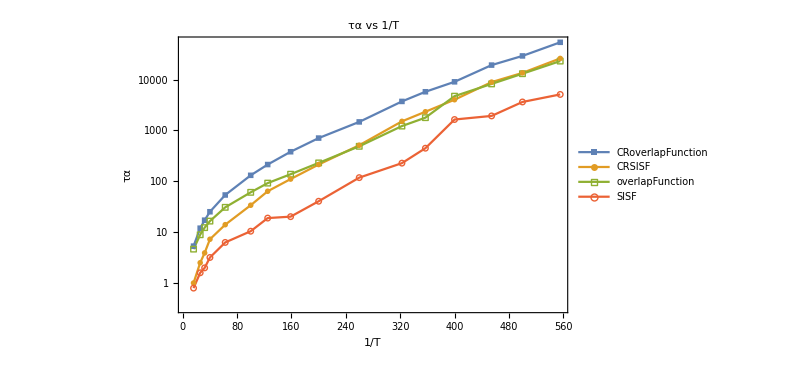

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/Tlist[[T]],tauCROverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauOverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■",Large],Style["●",Large],Style["□",Large],Style["○",Large]},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
tauTable=Prepend[Table[{Tlist[[T]],tauCROverlapfits[[T]],tauCRSISFfits[[T]],tauOverlapfits[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}],{"T","τα CRSISF","τα CR overlap","τα SISF","τα overlap"}]
```

{{T,τα CRSISF,τα CR overlap,τα SISF,τα overlap},{0.063,5.30434,0.999983,4.63605,0.793236},{0.039,11.9547,2.50014,8.88505,1.58599},{0.03105,17.1689,3.9034,12.259,1.98386},{0.025,25.1649,7.24834,16.4782,3.1748},{0.016,53.7381,14.011,30.7319,6.27555},{0.01,130.954,33.8089,60.6114,10.4212},{0.008,213.173,63.6444,92.052,18.8918},{0.0063,380.59,110.477,137.561,20.1574},{0.005,706.486,213.261,229.49,40.4621},{0.00385,1469.16,510.714,486.987,117.936},{0.0031,3714.56,1507.02,1217.13,227.173},{0.0028,5750.6,2327.63,1780.79,446.924},{0.0025,9021.89,4012.09,4710.57,1637.08},{0.0022,19230.9,8901.97,8204.43,1926.85},{0.002,29134.5,13519.1,13032.7,3623.88},{0.0018,53982.2,26010.6,23065.1,5095.46}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha_p380.jpeg",tauAlphafitingPlot];
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.809979,0.796758,0.809037,0.809862,0.80979,0.809928,0.80995,0.809939,0.809968,0.80997,0.809986,0.809967,0.809928,0.703551,0.771414,0.809972,0.809195,0.809984,0.793789,0.809994,0.809994,0.809994,0.794059}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.449978,0.437055,0.448006,0.449785,0.449754,0.449922,0.449957,0.449934,0.449975,0.449977,0.44999,0.449993,0.441588,0.473171,0.454078,0.449017,0.44834,0.455473,0.448606,0.457386,0.45083,0.452285,0.449566}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.529141,0.592079,0.569808,0.630995,0.641043,0.665991,0.691322,0.701875,0.704992,0.729689,0.738498,0.762204,0.759353,0.730815,0.74279,0.794476,0.764024,0.795187,0.765277,0.801778,0.865234,0.912167,0.836894}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.999912,0.999974,0.999974,0.999988,0.999992,0.999993,0.999996,0.999996,0.999997,0.999996,0.999997,0.999998,0.980185,0.993608,0.988459,0.976593,0.980814,0.978599,0.973606,0.976955,0.965694,0.961696,0.962681}

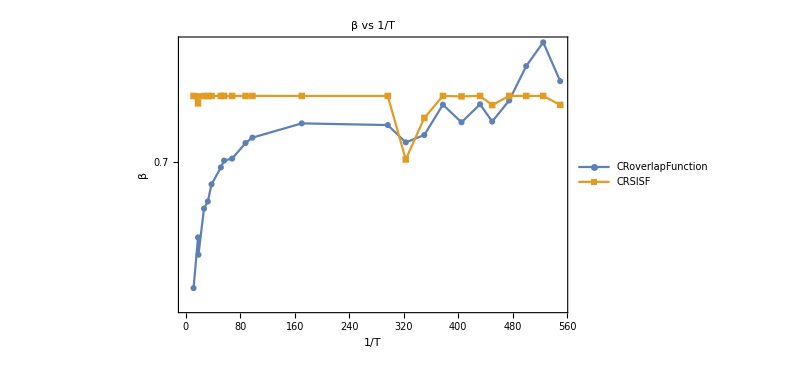

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingBeta_p380_p380.jpeg",betafitingPlot,ImageResolution->600];
```

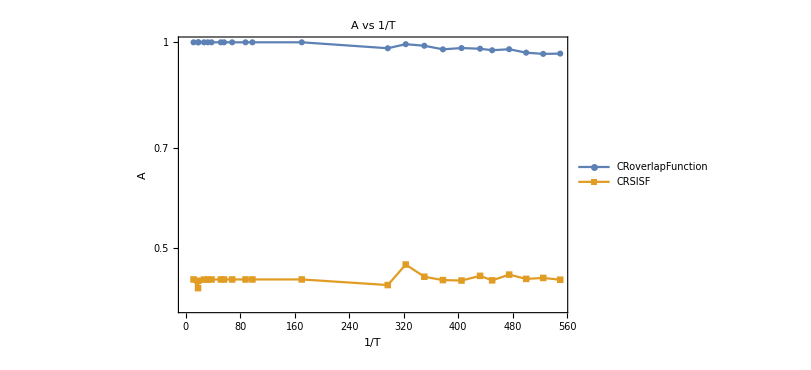

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingA_p380_p380.jpeg",GfitingPlot,ImageResolution->600];
```

```mathematica
tauCRSISFAllT
```

{0.728537,1.41524,1.61389,2.6929,4.03698,5.21129,9.19522,9.51448,14.8936,25.9793,32.3344,138.256,1036.02,1239.22,2019.54,2804.8,4144.73,5262.53,6834.04,9346.07,13224.1,18754.3,19569.1}

```mathematica
tauTable=Prepend[Table[{TlistAllT[[T]],tauCRSISFAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],{"T","τα CRSISF","τα CR overlap"}]
```

{{T,τα CRSISF,τα CR overlap},{0.08868,0.728537,3.16039},{0.05586,1.41524,6.7635},{0.05409,1.61389,6.75448},{0.03756,2.6929,12.5106},{0.03105,4.03698,17.4891},{0.02652,5.21129,23.0389},{0.01945,9.19522,38.8819},{0.01782,9.51448,42.9591},{0.01471,14.8936,64.5399},{0.01141,25.9793,101.84},{0.01023,32.3344,125.531},{0.005873,138.256,436.846},{0.003371,1036.02,2732.95},{0.00309559,1239.22,3582.02},{0.00285428,2019.54,5140.15},{0.00264787,2804.8,7160.55},{0.00246931,4144.73,10064.4},{0.0023133,5262.53,13246.9},{0.00222222,6834.04,17008.4},{0.00210526,9346.07,22594.2},{0.002,13224.1,29109.1},{0.00190476,18754.3,39352.1},{0.00181818,19569.1,46020.2}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv

```mathematica
NumberForm[#,{9,6},ExponentFunction->(Null&)]&/@TlistAllT
```

{0.088680,0.055860,0.054090,0.037560,0.031050,0.026520,0.019450,0.017820,0.014710,0.011410,0.010230,0.005873,0.003371,0.003096,0.002854,0.002648,0.002469,0.002313,0.002222,0.002105,0.002000,0.001905,0.001818}

```mathematica
TlistAllT
```

{0.08868,0.05586,0.05409,0.03756,0.03105,0.02652,0.01945,0.01782,0.01471,0.01141,0.01023,0.005873,0.003371,0.00309559,0.00285428,0.00264787,0.00246931,0.0023133,0.00222222,0.00210526,0.002,0.00190476,0.00181818}

```mathematica
TlistGeneral={0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}
```

{0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}

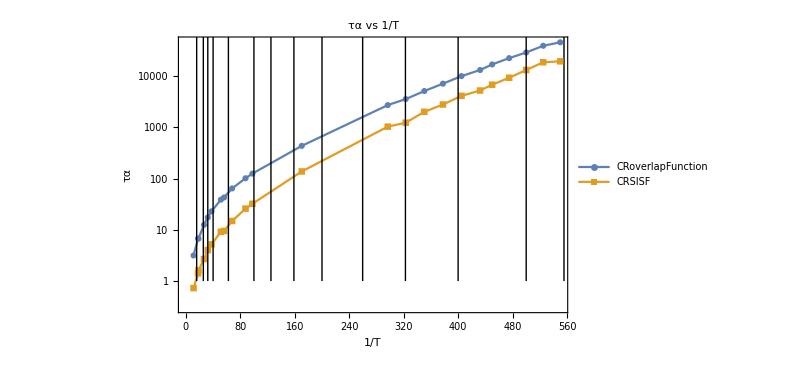

```mathematica
ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All,Epilog->Table[Line[{{1/TlistGeneral[[T]],0},{1/TlistGeneral[[T]],10000}}],{T,Length[TlistGeneral]}]]
```

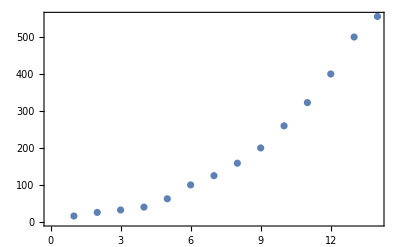

```mathematica
ListPlot[1/TlistGeneral]
```

```mathematica
tauEsGeneral={1.1841166706949628,2.462846296611076,3.8650575360708697,5.57413355409462,11.924841063370899,33.8105307104969,54.5761704083136,107.2953843344434,216.96587756816794,565.3189946945129,1243.945127271425,2065.,3731.3453237234366,7000.,12885.217184405017,22000.};
```

```mathematica
Length[TlistGeneral]
```

16